```mathematica
A = {
{p, x, y},
{0, p, z},
{0, 0, p}
};
```

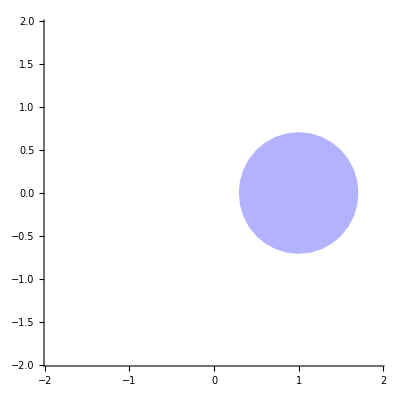

```mathematica
NumericalRangeVisual[A /. {p->1, x->0, y->1, z->1}]
```

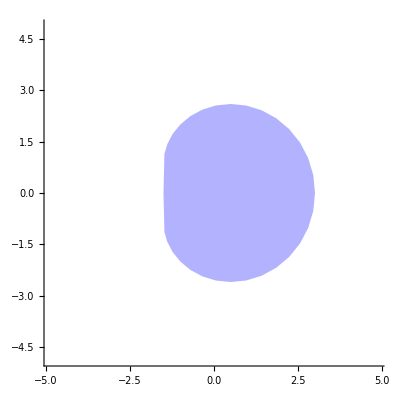

```mathematica
NumericalRangeVisual[A /. {p->0, x->3, y->3, z->3}]
```

```mathematica
{p, q, r} = Take[NumericalRange[A /. {p->0, x->2, y->1, z->2}], 3];
g = NumericalRangeVisual[A /. {p->0, x->2, y->1, z->2}];
```

```mathematica
Distance[{x1_, y1_}, {x2_, y2_}] := Sqrt[(x1-x2)^2 + (y1-y2)^2]
```

```mathematica
{cx, cy} = {x, y} /.Solve[{Distance[ComplexToReals[p], {x, y}] == Distance[ComplexToReals[q], {x, y}], Distance[ComplexToReals[p], {x, y}] == Distance[ComplexToReals[r], {x, y}]}, {x, y}] // First
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.161694,-0.000288519}

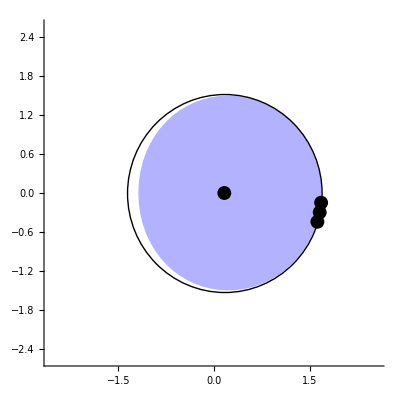

```mathematica
Show[Graphics[g], Graphics[{PointSize[0.025], Point[{ComplexToReals[p], ComplexToReals[q], ComplexToReals[r], {cx, cy}}]}],
Graphics[Circle[{cx, cy}, Distance[{cx, cy}, ComplexToReals[p]]]]
]
```

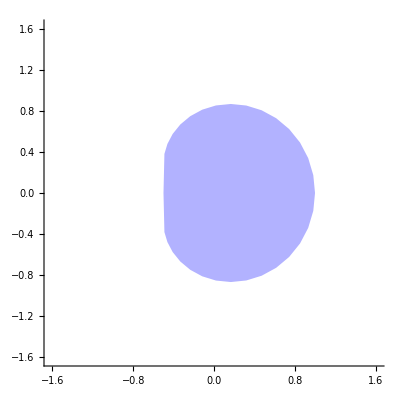

```mathematica
NumericalRangeVisual[{
{0, 1, 1},
{0, 0, 1},
{0, 0, 0}
}]
```